# Stability analyses under accelerating returns

```mathematica
Clear["Global`*"]; 
SetDirectory[NotebookDirectory[]];
```

## 1. Functions

```mathematica
blue=RGBColor["#0A71B7"]
orange= RGBColor["#D25F02"]
cm=72/2.54;
```

RGBColor[0.0392156862745098, 0.44313725490196076, 0.7176470588235294]

RGBColor[0.8235294117647058, 0.37254901960784315, 0.00784313725490196]

```mathematica
Functions = { Bc->Function[k,n (k/n)^u β]};
```

```mathematica
values={n->4,β->1,Cc-> 0.3,δ->1,u->0.75,cd-> 0.5} ;

cm=72/2.54;
```

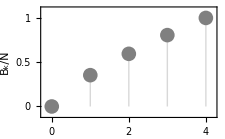

```mathematica
graphicspPayoffs=ListPlot[Table[{k,(k/n)^u β  }/.values,{k,0,4}],Filling->Axis,PlotStyle->Gray,Frame->True,FrameTicks->{{{0,0.5,1},None},{{0,1,2,3,4},None}},ImageSize->8cm,FrameLabel->{k,Rotate[Subscript[B, k]/N,-Pi/2]},LabelStyle->Directive[FontFamily->"Arial",FontSize->17,Black],PlotMarkers->{Automatic,15},PlotRange-> {{-0.2,4.2},{-0.1,1.1}}]
```

Figure 7 a of the main text

```mathematica
Export["Payoff_Sat.pdf",Show[graphicspPayoffs,ImageSize->8 cm]]
```

Payoff_Sat.pdf

## 2. Numerical analyses

Here we perform numerical stability analyses,looking for a value of x=(z,d_0,...,d_N) where directional selection is null on all traits. We also compute the singular value under unconditional dispersal(when d_0=d_1=...=d_N). To do so, we use the Mathematica function "FindRoot". This corresponds to the procedure described in section 3.4 of the main text and section D.3.1 of the Appendix. We also compute whether the singular strategy found is convergence stable by computing the eigenvalues if the Jacobian Matrix at the singular strategy (procedure described in Appendix D.3.2). Finally, we compute the eigenvalue of the Hessian Matrix to determine the evolutionary stability of the singular equilibrium(procedure described in Appendix D.3.3). We write the results obtained in a .txt file.

```mathematica
(*
	This script computes the singular strategy z^*=(Subscript[z, 1]^*,Subscript[z, 2]^*) reached by the population, and whether this strategy is evolutionary stable or if multiple morph will emerge. To run it, you will need to specify the parameter sets in the appropriate section below, and to give an explicit path and name for the output file that will be created.
*)
(************************** Parameters to be used ************************)
rangeu={0.35,0.65,0.75};
rangecd=Subdivide[0.05,0.95,18];
values={n->4,β->1.,Cc-> 0.3,δ->.1} ;
nval= n /. values;
βval=β/.values;
Ccval=Cc/.values;
δval=δ/.values;
valuesNeutral={n->nval,δ->0} ;
G = IdentityMatrix[nval+2];
G2=IdentityMatrix[2];

Functions = { Bc->Function[k,n(k/n)^u β]};

(****** Define the important functions *******)
Pk0[k_,z_,n_]:=z^k(1-z)^(n-k)Binomial[n,k];(* Probability that there is k cooperators among n individuals when the population is monomorphic for z *)
fec[k_,j_]:=(1+δ (Bc[k]/n-Cc j)); (* fecundity of an individual either cooperating (j=1) or defecting (j=0) in a group with k cooperators *)
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
(* average fecundity in a patch with k cooperators*)
fecphilo[k_]:=fecpatch[k](1-d[k]);(* offspring produced that will remain in their local patch *)
fecdisp[z_]:= ∑_(k2=0)^n d[k2] (1-cd) fecpatch[k2]Pk0[k2,z,n];
fecloc=( (1-d[1,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c1]/n+ (1-d[2,c1+c2+c3+c0]) fec[c1+c2+c3+c0,c2]/n+(1-d[3,c1+c2+c3+c0])fec[c1+c2+c3+c0,c3]/n+(1-d[c1+c2+c3+c0]) ((n-3-c0)fec[c1+c2+c3+c0,0]/n+c0 fec[c1+c2+c3+c0,1]/n) );
(* number of offspring coming into an arbirary patch when the population is monomorphic for z *)
m[k0_]:=fecdisp[d[n+1]] /(fecphilo[k0]+fecdisp[d[n+1]] )/.valuesNeutral;

monopop=Flatten[Table[{ d[i,k]-> d[k]},{k,0,nval+1},{i,1,3}]];
uncond1=Flatten[Table[{ d[i,k]-> d[i,0]},{k,0,nval},{i,1,3}]];
uncond2=Flatten[Table[{ d[k]-> d[0]},{k,0,nval} ]];
w=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 fec[c1+c2+c3+c0,c1]((  1-d[1,c1+c2+c3+c0])/(fecloc+ fecdisp[d[n+1]]) + ∑_(k0=0)^n ((d[1,c1+c2+c3+c0](1-cd) )/( fecphilo[k0]+ fecdisp[d[n+1]]))Pk0[k0,d[n+1],n])d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.Functions/.values;
(* Fitness of a focal individual*)

wP1=∑_(c0=0)^(n-3) ∑_(c3=0)^1 ∑_(c2=0)^1 ∑_(c1=0)^1 (fec[c1+c2+c3+c0,c1](  1-d[1,c1+c2+c3+c0])/(fecloc+ fecdisp[d[n+1]]))^2 d[1,n+1]^c1(1-d[1,n+1])^(1-c1) d[2,n+1]^c2(1-d[2,n+1])^(1-c2)d[3,n+1]^c3(1-d[3,n+1])^(1-c3) Pk0[c0,d[n+1],n-3]/.Functions/.values;
(* Average philopatric fitness, squared*)

R2 == ∑_(k0 =0)^n (1-m[k0])^2(1/n+((n-1)/n)R2)Pk0[k0,d[n+1],n]/.valuesNeutral;
solR2=Flatten[Solve[%,R2]];
solR2R={R2R->1/n+((n-1)/n)R2/.solR2};
R3 == ∑_(k0=0)^n (1-m[k0])^3(1/n^2+ 3((n-1)/n^2)R2+(((n-1)(n-2))/n^2)R3) Pk0[k0,d[n+1],n]/.valuesNeutral;
solR3=Flatten[Solve[%,R3]];
ΔR2dUncondi[x_]:=
R2R((1+(n-1)R2)D[wP1/.uncond1/.uncond2, d[1,x]] +(n-1)(2R2+(n-2)R3)D[wP1/.uncond1/.uncond2, d[2,x]])/. monopop /.solR2R/.solR3/. solR2  
ΔR2d [x_]:=
R2R((1+(n-1)R2)D[wP1, d[1,x]] +(n-1)(2R2+(n-2)R3)D[wP1, d[2,x]])/. monopop /.solR2R/.solR3/. solR2  ;
SUncondi=
Table[
D[w/.uncond1 /.uncond2, d[1,k]]+ (n-1)R2 D[w/.uncond1/.uncond2, d[2,k]]/. monopop /. solR2 /.uncond2/.values
,{k,{0,nval+1}}];
HUncondi=Table[D[w/.uncond1/.uncond2, d[1,x1],d[1,x2]]  + R2(n-1)   D[w/.uncond1/.uncond2, d[2,x1],d[2,x2]] +R2(n-1)   ( D[w/.uncond1/.uncond2, d[1,x1],d[2,x2]] + D[w/.uncond1/.uncond2,d[2,x1],d[1,x2]] ) + R3 (n-1)(n-2)  D[w/.uncond1/.uncond2,d[2,x1],d[3,x2]]+(n-1)D[w/.uncond1/.uncond2,d[2,x1]]ΔR2dUncondi[x2]+(n-1)D[w/.uncond1/.uncond2,d[2,x2]]ΔR2dUncondi[x1] /.monopop/.solR2R /.solR3/. solR2  /.values,{x1,{0,nval+1}},{x2,{0,nval+1}}]/. monopop /.uncond2/.values;

SCondi=Table[
D[w, d[1,x]]+ (n-1)R2 D[w, d[2,x]]/. solR2 /. monopop /.values
,{x,0,nval+1}];
HCondi=Table[D[w, d[1,x1],d[1,x2]]  + R2(n-1)   D[w, d[2,x1],d[2,x2]] +R2(n-1)   ( D[w, d[1,x1],d[2,x2]] + D[w,d[2,x1],d[1,x2]] ) + R3 (n-1)(n-2)  D[w,d[2,x1],d[3,x2]]+(n-1)D[w,d[2,x1]]ΔR2d[x2]+(n-1)D[w,d[2,x2]]ΔR2d[x1] /.monopop/.solR2R /.solR3/. solR2  /.values,{x1,0,nval+1},{x2,0,nval+1}];

(****** Creating the results file *******)
f="Saturating2_B_"<>TextString[βval]<>"_C_"<>TextString[Ccval]<>"_d_"<>TextString[δval]<>"_n_"<>TextString[nval]<>".txt"/.values;
If[!FileExistsQ[f], (* If it does not exist yet, create it and include a header with the name of columns *)
CreateFile[f];
Close[f] //Quiet;
stream=OpenAppend[f];
WriteLine[stream,"cd u dU zU J H d(n+1) z J H ds"];
];
Close[f] //Quiet;

Table[
d0baseline=2/(1+2 cd n+√(1+4 cd^2 (-1+n) n))/.values/.cd->cdtab;

(*unconditional dispersal*)
SUncondiTab=Evaluate[SUncondi/.cd->cdtab/.u->utab];equiUncondi0=FindRoot[Table[SUncondiTab[[i]]==0,{i,1,2}], {d[0],d0baseline,0,1},{d[nval+1],If[cdtab==rangecd[[1]],0.75,startz0 ]  }] ;
If[Max[ Last[equiUncondi0][[2]]]≤1&&Min[ Last[equiUncondi0][[2]]]≥0,
equiUncondi=equiUncondi0; 
JTabUncondi=D[SUncondiTab,{Table[ d[k],{k,{0,nval+1}}]}]/.equiUncondi;
JmaxUncondi=Re[Eigenvalues[JTabUncondi]]//Max;,
ΔzUncondi[u_]:=Clip[ u+G2.(SUncondiTab/. {d[0]->u⟦1⟧,d[5]->u⟦2⟧}),{0.,1.}];
inizUncondi = {d0baseline,0.4};
allzUncondi=NestWhile[ΔzUncondi,inizUncondi,EuclideanDistance[#1,#2]>10^-8>0.&,2,2000];
equiUncondi= {d[0]->allzUncondi⟦1⟧,d[5]->allzUncondi⟦2⟧};
JmaxUncondi=-1.;
];
startz0 = Last[equiUncondi][[2]];
d0 = First[equiUncondi][[2]];
HTabUncondi=HUncondi/.equiUncondi/.cd->cdtab/.u->utab;
HmaxUncondi=Eigenvalues[HTabUncondi]//Max;
If[cdtab==rangecd[[1]]||Evaluate[d[nval+1]/.equiCondi]==0.,
allval0=Append[ Table[ {d[k],d0baseline},{k,0,nval}] ,{d[nval+1],0.1   }];,
If[Evaluate[d[nval+1]/.equiCondi]==1.,
allval0=Append[ Table[ {d[k],d0baseline},{k,0,nval}] ,{d[nval+1],0.9  }];,allval0=Table[ {d[k],Evaluate[d[k]/.equiCondi]},{k,0,nval+1}]; ]];
SCondiTab=Evaluate[SCondi/.cd->cdtab/.u->utab];equiCondi0=FindRoot[Table[SCondiTab[[i]]==0,{i,1,nval+2}],allval0];testval = Table[d[k]/.equiCondi0,{k,0,nval+1}];
If[Max[testval]≤1&&Min[testval]≥0,
equiCondi=equiCondi0; 
JTabCondi=D[SCondiTab,{Table[ d[k],{k,0,nval+1}]}]/.equiCondi;
JmaxCondi=Re[Eigenvalues[JTabCondi]]//Max;,
Δz[u_]:=Clip[ u+G.(SCondiTab/. Table[d[k]-> u[[1+k]],{k,0,nval+1}] ),{0.,1.}];
ngenmax=5000;
iniz = Table[allval0[[k]][[2]],{k,1,nval+2}];
allz=NestWhile[Δz,iniz,EuclideanDistance[#1,#2]>10^-10&,2,ngenmax];
equiCondi=Table[d[x-1]->allz[[x]],{x,1,nval+2}];
JmaxCondi=-1.;
];
valz=Table[d[k]/.equiCondi,{k,0,nval+1}];
HTabCondi=HCondi/.equiCondi/.cd->cdtab/.u->utab;
(*remove all traits not at an intermediate value (still experiencing directional selection)*)
HTabCondi=Delete[HTabCondi,Flatten[{Position[valz,0.],Position[valz,1.]},1]];HTabCondi=Delete[Transpose[HTabCondi],Flatten[{Position[valz,0.],Position[valz,1.]},1]];
HmaxCondi=Eigenvalues[HTabCondi];
HmaxCondi=Delete[HmaxCondi,Position[HmaxCondi,0.]]//Max;
res=Flatten[{cdtab, utab,d0,startz0,JmaxUncondi,HmaxUncondi,Table[Round[d[k],0.000001]/.equiCondi,{k,0,nval+1} ] ,Round[JmaxCondi,0.000001],HmaxCondi,Round[Total[Chop@(Delete[SCondiTab/.equiCondi,Flatten[{Position[valz,0.],Position[valz,1.]},1]]) ],0.000001]}/.equiCondi];
stream=OpenAppend[f];
str=StringRiffle[res];
WriteLine[stream,str];
Close[f] //Quiet;,{utab,rangeu},{cdtab,rangecd}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}}

```mathematica
rangecd=Subdivide[0.01,0.99,98]
```

{0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3,0.31,0.32,0.33,0.34,0.35,0.36,0.37,0.38,0.39,0.4,0.41,0.42,0.43,0.44,0.45,0.46,0.47,0.48,0.49,0.5,0.51,0.52,0.53,0.54,0.55,0.56,0.57,0.58,0.59,0.6,0.61,0.62,0.63,0.64,0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,0.75,0.76,0.77,0.78,0.79,0.8,0.81,0.82,0.83,0.84,0.85,0.86,0.87,0.88,0.89,0.9,0.91,0.92,0.93,0.94,0.95,0.96,0.97,0.98,0.99}

## 3.Read the analyses (Fig 5a)

### 3.1 Evolution of cooperation

In this section we read the  . txt file obtained from the previous section and draw fig 8c of the main text and Fig S2d-e of the appendix .

```mathematica
rImport[βval_,Ccval_,δval_,nval_]:=Import["Saturating2_B_"<>TextString[βval]<>"_C_"<>TextString[Ccval]<>"_d_"<>TextString[δval]<>"_n_"<>TextString[nval]<>".txt","Table"];
ztrait[βval_,Ccval_,δval_,nval_,cdvect_,uval_]:=(
results=rImport[βval,Ccval,δval,nval];
results=Delete[results,1];
Listres=Select[results,#[[2]]==uval&];
traits=Table[a=Select[Listres,#[[1]]==cdi&];a,{cdi,cdvect}];
traits=Transpose[Flatten[traits,1]][[{1,4,-4}]]
);
dtrait[βval_,Ccval_,δval_,nval_,cdvect_,uval_]:=(
results=rImport[βval,Ccval,δval,nval];
results=Delete[results,1];
Listres=Select[results,#[[2]]==uval&];
traits=Table[a=Select[Listres,#[[1]]==cdi&];a,{cdi,cdvect}];
traits=Delete[Transpose[Flatten[traits,1]],{{1},{2},{3},{4},{5},{6},{6+nval+2},{6+nval+3},{6+nval+4},{6+nval+5}}]
);
```

```mathematica
cdv=Subdivide[0.05,0.95,18]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

```mathematica
PlotHelp[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
x0=ztrait[βval,Ccval,δval,nval,cdvect,uval];
p1=ListPlot[ Transpose[{cdvect,x0[[2]]}],PlotMarkers->Style[shape,size],PlotStyle->Gray,PlotRange->{{0,1.},{0.,1.0}}];
p2=ListPlot[  Transpose[{cdvect,x0[[3]]}],PlotMarkers->Style[shape,size],PlotStyle->orange];
Show[p1,p2,LabelStyle->Directive[FontFamily->" Arial",FontSize->12,Black],FrameTicks->{{{0,0.25,.5,0.75,1.},None},{{0,.5,1},None}},Frame->True,PlotRange->{{0,1.},{0.,1.05}},AspectRatio->0.85,FrameLabel->{None,"_"},RotateLabel->False])
```

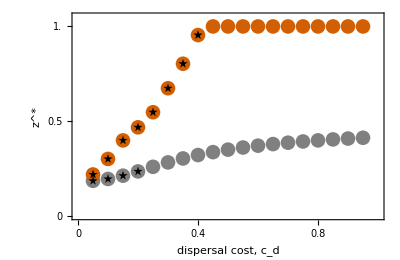

Sat_main.pdf

```mathematica
pmain=PlotHelp[1.0, 0.3,3.,4,cdv,0.75,●,15];
valsc=Delete[ztrait[1.0, 0.3,3.,4,cdv,0.75],2];
valsu=Delete[ztrait[1.0, 0.3,3.,4,cdv,0.75],3];
p1=ListPlot[Transpose[valsc][[1;;8]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,10]];
p3=ListPlot[Transpose[valsu][[1;;3]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,10]];
plot=Show[pmain,p1,p3,AspectRatio->0.65,FrameLabel->{"dispersal cost, c_d","z^*"},PlotRange->{{0,1},{0,1.05}},PlotRangePadding->0,FrameTicks->{{{0,.5,1.},None},{{0,0.2,0.4,0.6,0.8,1},None}},LabelStyle->Directive[FontFamily->" Arial",FontSize->15,Black]]
Export["Sat_main.pdf",plot,ImageSize->10.5cm]
```

```mathematica
p65=PlotHelp[1.0, 0.3,1.0,4,cdv,0.65,●,13];
p45=PlotHelp[1.0, 0.3,1.0,4,cdv,0.35,▲,14];
valsc=Delete[ztrait[1.0, 0.3,1.,4,cdv,0.65],2];
valsc2=Delete[ztrait[1.0, 0.3,1.,4,cdv,0.35],2];
p1=ListPlot[Transpose[valsc2][[11;;19]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
p2=ListPlot[Transpose[valsc][[6;;10]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
p3=ListPlot[Transpose[valsc][[1;;2]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
```

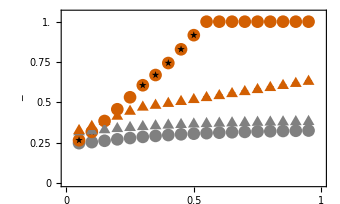

```mathematica
plot=Show[p65,p2,p3,p45,p1,AspectRatio->0.6,ImageSize->12cm]
```

```mathematica
Export["Sat_u.pdf",plot,ImageSize->12cm]
```

Sat_u.pdf

```mathematica
PlotH[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
x0=Hvals[βval,Ccval,δval,nval,cdvect,uval];
p2=ListLinePlot[  Transpose[{cdvect,x0[[2]]}],PlotStyle->orange];
Show[p2,LabelStyle->Directive[FontFamily->" Arial",FontSize->10,Black],FrameTicks->{{{0,0.02,.25,.5,0.75,1.},None},{{0,.5,1},None}},Frame->True,PlotRange->{{0.0,0.7},{-0.01,0.1}},AspectRatio->0.85,FrameLabel->{None,"z^*"},RotateLabel->False])
```

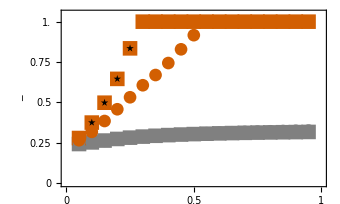

```mathematica
p4=PlotHelp[1.0, 0.3,1.0,4,cdv,0.65,●,13];
p6=PlotHelp[1.5, 0.3,1.0,6,cdv,0.65,■,15];
valsc=Delete[ztrait[1.0, 0.3,1.,4,cdv,0.65],2];
valsc2=Delete[ztrait[1.5, 0.3,1.,6,cdv,0.65],2];
p1=ListPlot[Transpose[valsc2][[1;;5]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
p3=ListPlot[Transpose[valsc][[6;;10]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
p2=ListPlot[Transpose[valsc][[1;;2]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
plot=Show[p6,p1,p4,p3,p2,AspectRatio->0.6,ImageSize->12cm]
```

```mathematica
Export["Sat_N.pdf",plot,ImageSize->12cm]
```

Sat_N.pdf

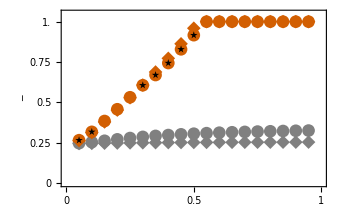

```mathematica
p15=PlotHelp[1.0, 0.3,1.,4,cdv,0.65,●,13];
p05=PlotHelp[1.0, 0.3,.1,4,cdv,0.65,◆,14];
valsc=Delete[ztrait[1.0, 0.3,1.,4,cdv,0.65],2];
valsc2=Delete[ztrait[1.0, 0.3,.1,4,cdv,0.65],2];
p1=ListPlot[Transpose[valsc2][[4;;10]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[☆,8]];
p3=ListPlot[Transpose[valsc][[6;;10]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
p2=ListPlot[Transpose[valsc][[1;;2]],PlotStyle->Black,AxesOrigin->{0,0},PlotMarkers->Style[★,8]];
plot=Show[p15,p05,p1,p2,p3,AspectRatio->0.6,ImageSize->12cm]
```

```mathematica
Export["Sat_delta.pdf",plot,ImageSize->12cm]
```

Sat_delta.pdf

### 3.1 Evolution of dispersal

In this section we read the  . txt file obtained from the numerical analyses and draw fig 8d of the main text and Fig S3 and S4 of the appendix .

```mathematica
rImport[βval_,Ccval_,δval_,nval_]:=Import["Saturating_B_"<>TextString[βval]<>"_C_"<>TextString[Ccval]<>"_d_"<>TextString[δval]<>"_n_"<>TextString[nval]<>".txt","Table"];
dtrait[βval_,Ccval_,δval_,nval_,cdvect_,uval_]:=(
results=rImport[βval,Ccval,δval,nval];
results=Delete[results,1];
Listres=Select[results,#[[2]]==uval&];
traits=Table[a=Select[Listres,#[[1]]==cdi&];a,{cdi,cdvect}];
traits=Delete[Transpose[Flatten[traits,1]],{{1},{2},{3},{4},{5},{6},{6+nval+2},{6+nval+3},{6+nval+4},{6+nval+5}}]
);
PlotDisp[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
x1=dtrait[βval,Ccval,δval,nval,cdvect,uval];
coop=Subdivide[nval,nval];
x2=Table[Transpose[{coop,Transpose[x1][[k]]}],{k,1,Length[cdvect]}];
plotdCondi=ListLinePlot[x2,PlotStyle->{{Dashed,Black,Thickness[0.002]}}];
plotdCondi2=ListPlot[x2,ColorFunction->mycolor,PlotMarkers->Style[shape,size]];
x=Show[{plotdCondi,plotdCondi2},LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Black],FrameTicks->{{{0,0.25,.5,0.75},None},{{0,1,2,3,4,5,6},None}},Frame->True,PlotRange->{{0,nval},{0,0.75}},AspectRatio->0.75,FrameLabel->{"k","d^*"},RotateLabel->False])
PlotPhil[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
Functions = { Bc->Function[k,n(k/n)^u β]};
fecpatch[k_]:=(1+ δ((k /n)(Bc[k]/n-Cc )+(1-k/n)(Bc[k]/n)));
x1=dtrait[βval,Ccval,δval,nval,cdvect,uval];
coop=Subdivide[nval,nval];
fecall=Table[fecpatch[i],{i,0,nval}]/.Functions/.u->uval/.n->nval/.β->βval/.Cc->Ccval/.δ->δval;
x2=Table[Transpose[{coop,Transpose[fecall(1-x1)][[k]]}],{k,1,Length[cdvect]}];
x3=Table[Transpose[{coop,Transpose[fecall]}],{k,1,Length[cdvect]}];
plotdCondi=ListLinePlot[x2,PlotStyle->{{Dashed,Black,Thickness[0.002]}}];
plotdCondi2=ListPlot[x2,ColorFunction->mycolor,PlotMarkers->Style[shape,size]];
plotfec=ListLinePlot[x3,PlotStyle->{{Dashed,Black,Thickness[0.002]}}];
plotfec2=ListPlot[x3,PlotStyle->Black,PlotMarkers->Style[shape,size]];
x=Show[{plotdCondi,plotdCondi2,plotfec,plotfec2},LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Black],FrameTicks->{{{.5,1.,1.5},None},{{0,1,2,3,4,5,6},None}},Frame->True,PlotRange->{{0,nval},{0.45,2}},AspectRatio->0.75,FrameLabel->{"k","f"},RotateLabel->False])
```

```mathematica
PlotDispcol2[βval_,Ccval_,δval_,nval_,cdvect_,uval_]:=(
listc=Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(6)]]]];
mycolor=Function[{x,y},listc[[(x*nval)+1]]];
x1=dtrait[βval,Ccval,δval,nval,cdvect,uval];
coop=Subdivide[nval,nval];
x2=Table[Transpose[{coop,Transpose[x1][[k]]}],{k,1,Length[cdvect]}];
plotdCondi=ListLinePlot[x2,PlotStyle->{{Dashed,Black,Thickness[0.003]}}];
plotdCondi2=ListPlot[x2,ColorFunction->mycolor,PlotStyle->PointSize[0.06] ];
x=Show[{plotdCondi,plotdCondi2},LabelStyle->Directive[FontFamily->"Arial",FontSize->15,Black],FrameTicks->{{{0,0.5,1.},None},{{0,1,2,3,4,5,6},None}},Frame->True,PlotRange->{{0,nval},{0,1}},AspectRatio->0.75,FrameLabel->{"k","d^*"},RotateLabel->False])
```

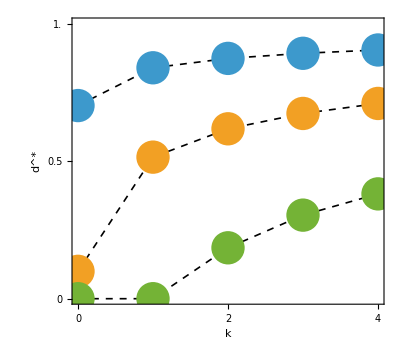

disp_main.pdf

```mathematica
pd=Show[PlotDispcol2[1.,0.3,3.,4,{0.05,0.15,0.35},0.75],AspectRatio->0.9,PlotRangePadding->{0.18,0.05}]
Export["disp_main.pdf",pd,ImageSize->7.62cm]
```

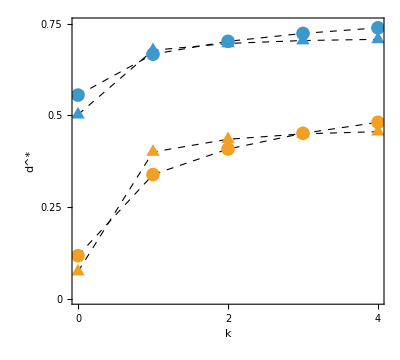

```mathematica
p45=PlotDisp[1.,0.3,1.,4,{0.1,0.25},0.35,▲,16];
p75=PlotDisp[1.,0.3,1.,4,{0.1,0.25},0.65,●,14];
plot=Show[p45,p75,AspectRatio->0.9]
```

```mathematica
Export["disp_u.pdf",plot,ImageSize->12cm]
```

disp_u.pdf

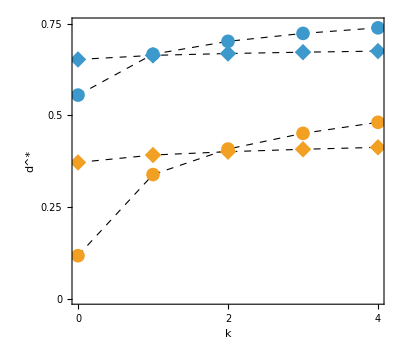

disp_delta.pdf

```mathematica
p65=PlotDisp[1.,0.3,.1,4,{0.1,0.25},0.65,◆,17];
p75=PlotDisp[1.,0.3,1.,4,{0.1,0.25},0.65,●,14];
plot=Show[p75,p65,AspectRatio->0.9]
Export["disp_delta.pdf",plot,ImageSize->12cm]
```

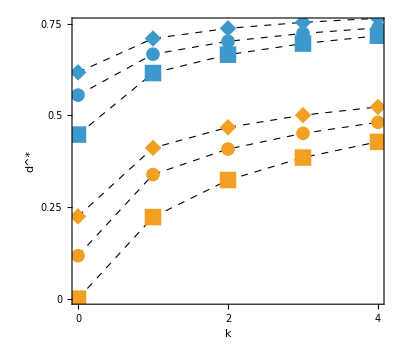

```mathematica
p65=PlotDisp[1.25,0.3,1.,4,{0.1,0.25},0.65,■,17];
pc=PlotDisp[1.,0.375,1.,4,{0.1,0.25},0.65,◆,17];
pb=PlotDisp[1.,0.3,1.,4,{0.1,0.25},0.65,●,14];
plot=Show[pb,pc,p65,AspectRatio->0.9]
```

```mathematica
Export["disp_B.pdf",plot,ImageSize->12cm]
```

disp_B.pdf

```mathematica
PlotDispf[βval_,Ccval_,δval_,nval_,cdvect_,uval_,shape_,size_]:=(
listc=Map[Lighter[blue,#]&,Reverse[Range[0,0.8,N[0.8/(6)]]]];
mycolor=Function[{x,y},listc[[(x*nval)+1]]];
x1=dtrait[βval,Ccval,δval,nval,cdvect,uval];
coop=Subdivide[1,nval];
x2=Table[Transpose[{coop,Transpose[x1][[k]]}],{k,1,Length[cdvect]}];
plotdCondi=ListLinePlot[x2,PlotStyle->{{Dashed,Black,Thickness[0.002]}}];
plotdCondi2=ListPlot[x2,ColorFunction->mycolor,PlotMarkers->Style[shape,size]];
x=Show[{plotdCondi,plotdCondi2},LabelStyle->Directive[FontFamily->"Arial",FontSize->12,Black],FrameTicks->{{{0,0.25,.5,0.75},None},{{0,0.5,1},None}},Frame->True,PlotRange->{{0,1},{0,0.75}},AspectRatio->0.75,FrameLabel->{"k","d^*"},RotateLabel->False])
```

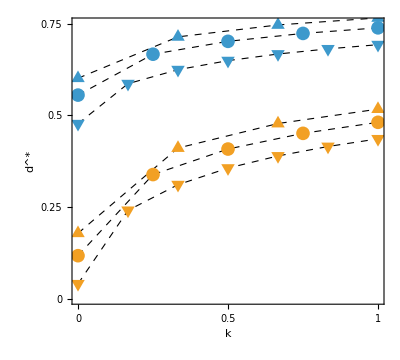

```mathematica
p3=PlotDispf[1.,0.3,1.,3,{0.1,0.25},0.65,▲,16];
p4=PlotDispf[1.,0.3,1.,4,{0.1,0.25},0.65,●,14];
p6=PlotDispf[1.,0.3,1.,6,{0.1,0.25},0.65,▼,16];
plot=Show[p3,p4,p6,AspectRatio->0.9]
```

```mathematica
Export["disp_N.pdf",plot,ImageSize->12cm]
```

disp_N.pdf

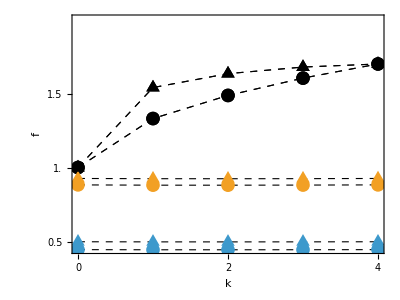

```mathematica
pf=Show[PlotPhil[1.,0.3,1.,4,{0.1,0.25},0.65,●,14],PlotPhil[1.,.3,1.,4,{0.1,0.25},0.35,▲,16]]
```

```mathematica
Export["f_df.pdf",pf,ImageSize->12cm]
```

f_df.pdf